2.18896-1.99494 x

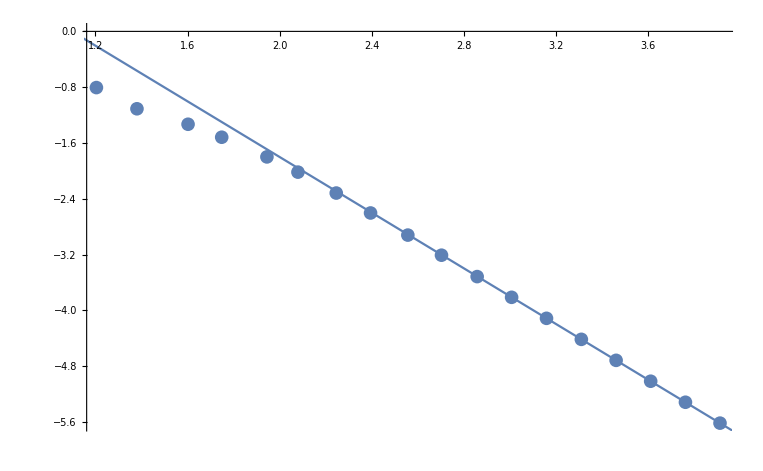

```mathematica
output={
{0016,0.1565486791047669},{0024,0.0777617121470163},{0040,0.0466636284498040},{0056,0.0304079452738043},{0088,0.0158847098136848},{0120,0.0096109986639444},{0176,0.0048188244957727},{0248,0.0024964096227872},{0360,0.0012033421883262},{0504,0.0006196708488851},{0720,0.0003058518734191},{1016,0.0001544089143977},{1440,0.0000771739367516},{2040,0.0000385682856367},{2888,0.0000192873009715},{4080,0.0000096808095715},{5776,0.0000048380950272},{8160,0.0000024287814577}

};
f=Normal@LinearModelFit[Log10@output⟦-4;;-1⟧,{x},x]
Show[ListPlot@Log10@output,Plot[f,{x,0,4}]]
```

```mathematica
E^7.
```

1096.63

```mathematica
{8,0.0002346446549774},{16,0.0000107755524099},{32,0.0000005743324006},{64,0.0000000649786230},{128,0.0000000410900667},{256,0.0000000290899905},{512,0.0000000205784033},{1024,0.0000000147364712},
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Chengzhe\Desktop\LIS2T\20181128_Zhou_Troian_JFMRapids_DynamicTaylorCone\Code\spline\Output

{{0,0.19635,0},{0.0980171,0.195404,-0.00377886},{0.19509,0.192577,-0.00752136},{0.290285,0.187895,-0.0111914},{0.382683,0.181403,-0.0147537},{0.471397,0.173165,-0.0181738},{0.55557,0.163259,-0.021419},{0.634393,0.15178,-0.0244578},{0.707107,0.13884,-0.0272612},{0.77301,0.124563,-0.0298019},{0.83147,0.109086,-0.0320558},{0.881921,0.0925585,-0.0340008},{0.92388,0.0751397,-0.0356185},{0.95694,0.0569973,-0.036893},{0.980785,0.0383059,-0.0378124},{0.995185,0.0192456,-0.0383674},{1,-1.11814×10^-16,-0.0385532},{0.995185,-0.0192456,-0.0383674},{0.980785,-0.0383059,-0.0378124},{0.95694,-0.0569973,-0.036893},{0.92388,-0.0751397,-0.0356185},{0.881921,-0.0925585,-0.0340008},{0.83147,-0.109086,-0.0320558},{0.77301,-0.124563,-0.0298019},{0.707107,-0.13884,-0.0272612},{0.634393,-0.15178,-0.0244578},{0.55557,-0.163259,-0.021419},{0.471397,-0.173165,-0.0181738},{0.382683,-0.181403,-0.0147537},{0.290285,-0.187895,-0.0111914},{0.19509,-0.192577,-0.00752136},{0.0980171,-0.195404,-0.00377886},{2.39392×10^-16,-0.19635,2.0331×10^-15},{1,-1.98254×10^-18,-0.0385532},{0.995185,-0.0192456,-0.0383674},{0.980785,-0.0383059,-0.0378124},{0.95694,-0.0569973,-0.036893},{0.92388,-0.0751397,-0.0356185},{0.881921,-0.0925585,-0.0340008},{0.83147,-0.109086,-0.0320558},{0.77301,-0.124563,-0.0298019},{0.707107,-0.13884,-0.0272612},{0.634393,-0.15178,-0.0244578},{0.55557,-0.163259,-0.021419},{0.471397,-0.173165,-0.0181738},{0.382683,-0.181403,-0.0147537},{0.290285,-0.187895,-0.0111914},{0.19509,-0.192577,-0.00752136},{0.0980171,-0.195404,-0.00377886},{6.12323×10^-17,-0.19635,-2.57793×10^-17},{-0.0980171,-0.195404,0.00377886},{-0.19509,-0.192577,0.00752136},{-0.290285,-0.187895,0.0111914},{-0.382683,-0.181403,0.0147537},{-0.471397,-0.173165,0.0181738},{-0.55557,-0.163259,0.021419},{-0.634393,-0.15178,0.0244578},{-0.707107,-0.13884,0.0272612},{-0.77301,-0.124563,0.0298019},{-0.83147,-0.109086,0.0320558},{-0.881921,-0.0925585,0.0340008},{-0.92388,-0.0751397,0.0356185},{-0.95694,-0.0569973,0.036893},{-0.980785,-0.0383059,0.0378124},{-0.995185,-0.0192456,0.0383674},{-1,-2.84495×10^-16,0.0385532}}

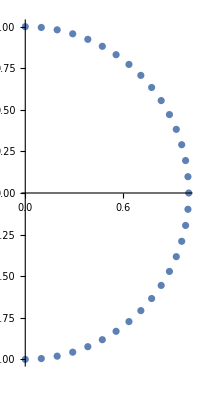

```mathematica
data=Import["tt.txt","Data"]
r=data⟦1;;Length@data/2⟧;
z=data⟦Length@data/2+1;;-1⟧;
ListPlot[Transpose@{r⟦All,1⟧,z⟦All,1⟧},AspectRatio->Automatic]
```

```mathematica
m
```

m

```mathematica
{EllipticK[0.999],EllipticE[0.999]}
NumberForm[%,{17,17}]
```

{4.84113,1.00217}

{4.84113256055029500,1.00217079083444400}